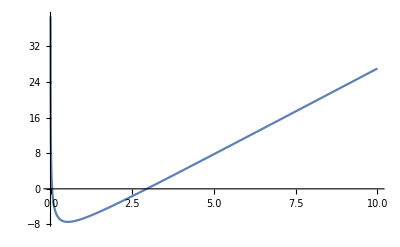

```mathematica
(*Зададим праую часть уравнения и построим ее график*)
f[x_]=4*x+Log[x]^2-4*Sqrt[1+x]-5;
Plot[f[x],{x,0.001,10}]
```

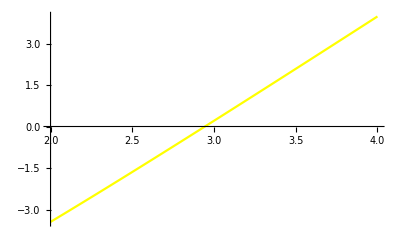

```mathematica
(*Локализуем правый корень уравнения*)
A=2;
B=4;
G=Plot[f[x],{x,A,B},PlotStyle->Yellow]
```

```mathematica
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим отрезок локализации корня*)
a=A;
b=B;
(*Найдем количество приближений к корню, используя априорную оценку*)
n=Floor[Log[2,(b-a)/ϵ]]+1;
(*Зададим переменную для хранения приближений к корню уравнения*)
It=List[];
(*Зададим переменную для хранения концов отрезков*)
Segments={{a,b}};
(*Реализуем алгоритм метода половинного деления*)
For[i=1,i≤n,i++,
c=(a+b)/2;
It=AppendTo[It,{c,0}];
If[f[c]==0,Break[]];
If[f[a]*f[c]<0,b=c,a=c];
Segments=AppendTo[Segments,{a,b}]
]
Print["Корень уравнения равен: ",N[c]]
Print["Количество приближений равно: ",n]
```

Корень уравнения равен: 2.94434

Количество приближений равно: 11

```mathematica
(*Выполним анимацию приближений к корню*)
Animate[Show[G,Plot[0,{x,Segments[[k,1]],Segments[[k,2]]},PlotStyle->Orange],ListPlot[{It[[k]]},PlotStyle->Red]],{k,1,n,1},AnimationRunning->False]
```

```mathematica
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим отрезок локализции корня*)
a=A;
b=B;
(*Разделим отрезок локализации корня в отношении золотого сечения слева*)
c=a+(3-Sqrt[5])/2*(b-a);
(*Зададим переменную для подсчёта количества приближений*)
n=1;
(*Зададим переменную для хранения приближений к корню уравнения*)
It={{c,0}};
(*Зададим переменную для хранения концов отрезков*)
Segments={{a,b}};
(*Реализуем алгоритм метода золотого сечения*)
While[b-a≥ϵ,
If[f[c]==0,Break[]];
If[f[a]*f[c]<0,b=c,a=c];
c=a+(3-Sqrt[5])/2*(b-a);
n=n+1;
It=AppendTo[It,{c,0}];
Segments=AppendTo[Segments,{a,b}]
]
Print["Корень уравнения равен: ",N[c]]
Print["Количество приближений к корню равно: ",n]
```

Корень уравнения равен: 2.94462

Количество приближений к корню равно: 10

```mathematica
(*Выполним анимацию приближений к корню*)
Animate[Show[G,Plot[0,{x,Segments[[k,1]],Segments[[k,2]]},PlotStyle->Orange],ListPlot[{It[[k]]},PlotStyle->Red]],{k,1,n,1},AnimationRunning->False]
```

```mathematica
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим отрезок локализции корня*)
a=A;
b=B;
(*Разделим отрезок локализации корня в отношении золотого сечения справа*)
c=b-(3-Sqrt[5])/2*(b-a);
(*Зададим переменную для подсчёта количества приближений*)
n=1;
(*Зададим переменную для хранения приближений к корню уравнения*)
It={{c,0}};
(*Зададим переменную для хранения концов отрезков*)
Segments={{a,b}};
(*Реализуем алгоритм метода золотого сечения*)
While[b-a≥ϵ,
If[f[c]==0,Break[]];
If[f[a]*f[c]<0,b=c,a=c];
c=b-(3-Sqrt[5])/2*(b-a);
n=n+1;
It=AppendTo[It,{c,0}];
Segments=AppendTo[Segments,{a,b}]
]
Print["Корень уравнения равен: ",N[c]]
Print["Количество приближений к корню равно: ",n]
```

Корень уравнения равен: 2.94483

Количество приближений к корню равно: 15

```mathematica
(*Выполним анимацию приближений к корню*)
Animate[Show[G,Plot[0,{x,Segments[[k,1]],Segments[[k,2]]},PlotStyle->Orange],ListPlot[{It[[k]]},PlotStyle->Red]],{k,1,n,1},AnimationRunning->False]
```

```mathematica
(*Зададим точность вычислений*)
ϵ=10^(-3);
(*Зададим отрезок локализации корня*)
a=A;
b=B;
(*Найдем точку пересечения хорды графика функции с осью абсцисс*)
c1=(a*f[b]-b*f[a])/(f[b]-f[a]);
(*Зададим предыдущее приближение к корню*)
c2=a;
(*Зададим переменную для хранения приближений к корню уравнения*)
It={{c1,0}};
(*Зададим переменную для хранения концов отрезков*)
Segments={{a,b}};
(*Зададим переменную для хранения хорд графика функции*)
Chord={(f[b]-f[a])*(x-a)/(b-a)+f[a]};
(*Зададим переменную для подсчёта количества приближений*)
n=1;
While[Abs[c1-c2]≥ϵ,
If[f[c1]==0,Break[]];
If[f[a]*f[c1]<0,b=c1,a=c1];
c2=c1;
c1=(a*f[b]-b*f[a])/(f[b]-f[a]);
It=AppendTo[It,{c1,0}];
Segments=AppendTo[Segments,{a,b}];
Chord=AppendTo[Chord,{(f[b]-f[a])*(x-a)/(b-a)+f[a]}];
n=n+1
]
Print["Корень уравнения равен: ",N[c1]]
Print["Количество приближений к корню равно: ",n]
```

Корень уравнения равен: 2.94451

Количество приближений к корню равно: 3

```mathematica
(*Выполним анимацию приближений к корню*)
Animate[Show[G,Plot[0,{x,Segments[[k,1]],Segments[[k,2]]},PlotStyle->Orange],Plot[Chord[[k]],{x,A,B}],ListPlot[{It[[k]]},PlotStyle->Red]],{k,1,n,1},AnimationRunning->False]
```